# Zika vaccine MS results

```mathematica
Quit[]
```

## Setup

### Headers

```mathematica
If[$CommandLine[[2]]=="-wstp",ClusterRun=False,ClusterRun=True];
```

```mathematica
If[ClusterRun,SetDirectory["./"],SetDirectory[NotebookDirectory[]]];
```

```mathematica
Import["Zika vaccine model setup.m"]
```

## Figure 1 - Plot time series

### Setup

#### Read in data

```mathematica
SetDirectory[NotebookDirectory[]<>"/GeneratedResults/VaccineImpactTimeSeries"]
```

C:\Users\carbon\Dropbox\Code\Git\ZikaVaccineModel\GeneratedResults\VaccineImpactTimeSeries

```mathematica
vaccineTimeSeriesScenarios=Get["vaccineTimeSeriesScenarios.dat"];
```

#### Setup plots

```mathematica
Clear@plotFigure1
plotFigure1[data_,outcome_,legend_,cumulative_:False,yrange_:All,ysteps_:Automatic,xrange_:{0,3*52}]:=ListLinePlot[If[cumulative,#[outcome],Differences[#[outcome]]]&/@Values[data],
PlotRange->{xrange,yrange},PlotLegends->legend,
PlotStyle->{Directive[Black,Dashed],Black,Directive[Black,Dotted],Directive[Black,DotDashed],Directive[Black,Dashing]},
LabelStyle->Directive[Black,16],

Frame->{True,True,False,False},
FrameStyle->Black,
FrameLabel->{"Year","Infections"},
FrameTicks->{{If[ysteps==Automatic,Automatic,Range[yrange[[1]],yrange[[2]],ysteps]],None},{{#,#/52}&/@Range[52,52*3,52],None}},

ImageSize->{Automatic,200}
]
```

### Plot “best fit”

#### Plot all infections

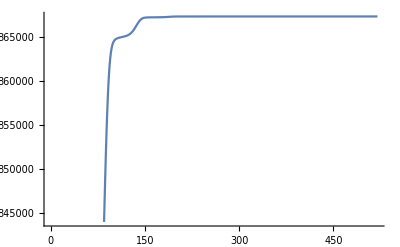

```mathematica
ListLinePlot@vaccineTimeSeriesScenarios["NoVaccination"]["allInfections"]
```

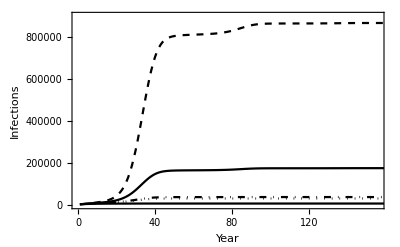

```mathematica
plotFigure1[vaccineTimeSeriesScenarios,"allInfections",None,True,{0,900000},300000]
```

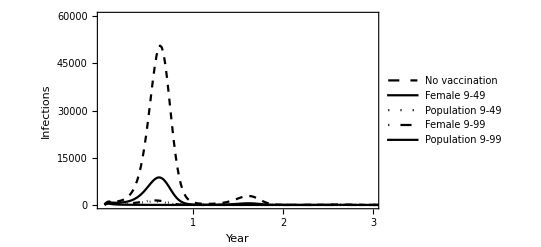

```mathematica
plotFigure1[vaccineTimeSeriesScenarios,"allInfections",{"No vaccination","Female 9-49","Population 9-49","Female 9-99","Population 9-99"},False,{0,60000},20000]
```

#### Plot prenatal infections infections

```mathematica
Keys@vaccineTimeSeriesScenarios
```

{NoVaccination,WHOfemale,WHOall,allfemale,allpopulation}

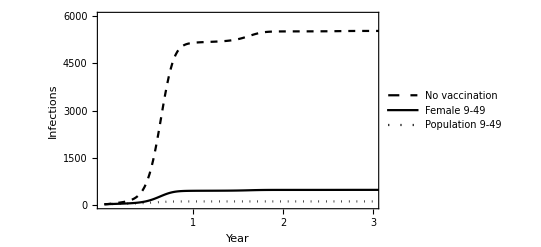

```mathematica
Show[
plotFigure1[vaccineTimeSeriesScenarios[[;;3]],"prenatalInfections",{"No vaccination","Female 9-49","Population 9-49","Female 9-99","Population 9-99"}[[;;3]],True,{0,6000},2000],
Graphics[Text[Style["A",Bold,16],{-10,100}]]
]
```

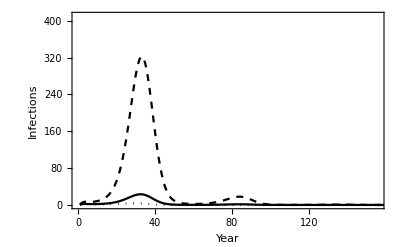

```mathematica
plotFigure1[vaccineTimeSeriesScenarios[[;;3]],"prenatalInfections",None,False,{0,410},100]
```

## Figure 3 - Plot contour scenarios

### Setup

#### Read in results

```mathematica
SetDirectory[NotebookDirectory[]<>"GeneratedResults/PriorRcontours"]
contourResults=Association[(#->Get["results_"<>#<>".dat"])&/@{"Puerto Rico"}(*CountryNames*)];
SetDirectory[NotebookDirectory[]];
```

C:\Users\carbon\Dropbox\Code\Git\ZikaVaccineModel\GeneratedResults\PriorRcontours

```mathematica
skipFunc=Function[data,data["attR"]==0.35||data["attR"]>0.5]
```

Function[data,data[attR]==0.35||data[attR]>0.5]

```mathematica
MinMax[#["attR"]&/@contourResults["Puerto Rico"]]
```

{0.05,0.55}

```mathematica
attRRange=Sort@DeleteDuplicates[#["attR"]&/@contourResults["Puerto Rico"]]
```

{0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55}

```mathematica
vrateRange=Sort@DeleteDuplicates[#["vrate"]&/@contourResults["Puerto Rico"]]
```

{0,0.5,0.9}

```mathematica
priorRRange=Sort@DeleteDuplicates[#["priorR"]&/@contourResults["Puerto Rico"]]
```

{0.,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95}

#### Add in 0 attack rate data for contour plotting

```mathematica
contourResults["Puerto Rico"]=Join[contourResults["Puerto Rico"],Flatten[Table[Association[{"attR"->attR,"vrate"->vrate,"priorR"->priorR,
"Results"->
With[{dummyResult=First[Select[contourResults["Puerto Rico"],(#["vrate"]==vrate&&#["priorR"]==priorR)&]]["Results"]},
Association[{"vaccines"->dummyResult["vaccines"],"prenatalInfections"->0.1,"pregnancies"->dummyResult["pregnancies"],"population"->dummyResult["population"]}]
]
}
],{attR,{0}},{vrate,vrateRange},{priorR,priorRRange}]]];
```

#### Define functions

```mathematica
Clear[extractContour]
extractContour[data_,contourIn_]:=With[{toret=Flatten[Cases[Normal@ListContourPlot[data,Contours->{contourIn},PlotRange->{0,Max[data]}],Tooltip[contour_,label_]:>Cases[contour,l_Line:>ArrayPad[First@l,{{0},{0,1}},label]],Infinity],1]},
If[toret=={},{},toret[[1,All,{1,2}]]]]
```

```mathematica
Clear@plotAttrContour
plotAttrContour[country_,vrate_,contours_,colorscheme_,maxCont_:0,minContour_:0.5,labelsize_:16,contourlabelsize_:12,plotlabel_:"",xlabel_:"",ylabel_:"",xrange_:{0,0.5},yrange_:{0,0.5}]:=
With[{data={#["attR"],#["priorR"],1000*#["Results"]["prenatalInfections"]/#["Results"]["pregnancies"]}&/@Select[contourResults[country],(#["vrate"]==vrate&&!skipFunc[#])&]},
With[{
maxContour=If[maxCont==0,Floor[Max[Flatten[data[[All,3]]]]*1.2],maxCont]
},
Show[

ListLinePlot[
Sow[(With[{calldata=extractContour[data,#]},
If[calldata=={},Nothing,Callout[calldata,Style[ToString[#],contourlabelsize]]]]&/@contours)],PlotStyle->None,AspectRatio->1,PlotRange->{xrange,yrange},##],

ListContourPlot[data,
Contours->contours,ContourStyle->None,ColorFunctionScaling->False,
ColorFunction->(ColorData[colorscheme][((Log[#]-Log[minContour])/(Log[maxContour]-Log[minContour]))]&),
ClippingStyle->Automatic,PlotRange->{xrange,yrange,All},
RegionFunction->Function[{x,y,z},xrange[[1]]≤x≤xrange[[2]]&&yrange[[1]]≤y≤yrange[[2]]],

##],

PlotRange->{xrange,yrange}

]&[
PlotLabel->plotlabel,

Frame->{True,True,False,False},FrameStyle->Black,FrameLabel->{xlabel,ylabel},
FrameTicks->{{{#,ToString[Floor[100*#]]<>"%"}&/@{yrange[[1]],Mean@yrange,yrange[[2]]},None},{{#,ToString[Floor[100*#]]<>"%"}&/@{xrange[[1]],Mean@xrange,xrange[[2]]},None}},

ImageSize->250,

LabelStyle->Directive[Black,labelsize],
ImagePadding->{{60,40},{60,0}}
]
]
]
```

```mathematica
Clear[barLegend]
barLegend[maxContour_,colorscheme_,labelsize_,minContour_,contourlabelsteps_]:=BarLegend[{(ColorData[colorscheme][1-#(*(Log[#]-Log[0.1])/(Log[1000]-Log[0.1])*)]&),{0,1}},LegendLabel->" Zika infections per
  1000 pregnancies",LabelStyle->Directive[Black,Alignment->Center,labelsize],Ticks->With[{tickReplace=({#,If[#≥1.0,Round[#],#]&[Exp[#*(Log[(*1000*)maxContour]-Log[minContour])+Log[minContour]]]}&/@contourlabelsteps)},Transpose[{tickReplace[[All,1]],Reverse[tickReplace[[All,2]]]}]]]
```

```mathematica
Clear[MasterPlotFigure2]
MasterPlotFigure2[country_,label_:True]:=With[{colorscheme={"CherryTones","Reverse"},contours={5,10,25,100,200,400(*5,10,25,50,100,200,350*)},maxCont=500,minContour=0.5,labelsize=16,contourlabelsize=12,xlabel="Attack rate",ylabel="Existing immunity",
contourlabelsteps=Range[0,1,1/3]},

Labeled[
Show[
Legended[
GraphicsRow[
{
plotAttrContour[country,0,contours,colorscheme,maxCont,minContour,labelsize,contourlabelsize,"No vaccination","",ylabel],
plotAttrContour[country,0.5,contours,colorscheme,maxCont,minContour,labelsize,contourlabelsize,"50% coverage",xlabel,""]
(*},
{
plotAttrContour[country,0.7,contours,colorscheme,maxCont,minContour,labelsize,contourlabelsize,"70% coverage",xlabel,ylabel]*),
plotAttrContour[country,0.9,contours,colorscheme,maxCont,minContour,labelsize,contourlabelsize,"90% coverage","",""]
}
],barLegend[maxCont,colorscheme,labelsize,minContour,contourlabelsteps]],
Graphics[Text[Style["A",Bold,labelsize],{21,-37}]],
Graphics[Text[Style["B",Bold,labelsize],{285,-37}]],
Graphics[Text[Style["C",Bold,labelsize],{555,-37}]](*,
Graphics[Text[Style["D",Bold,labelsize],{285,-303}]]*)
],
If[label,Text[Style[country,Bold,labelsize]],""],Top]
]
```

### Plots

#### Plot Puerto Rico

```mathematica
MasterPlotFigure2["Puerto Rico",False]
```

-Graphics-

### Extract specific results

#### 25% attack rate

```mathematica
Table[
vrate->With[{res=
Select[contourResults["Puerto Rico"],(
#["attR"]==0.25&&#["vrate"]==vrate&&#["priorR"]==0.25
)&][[1]]["Results"]},
res["prenatalInfections"]/res["pregnancies"]*1000],
{vrate,{0.5,0.9}}
]
```

{0.5→5.19872,0.9→2.05964}

```mathematica
With[{res=
Select[contourResults["Puerto Rico"],(
#["attR"]==0.25&&#["vrate"]==0&&#["priorR"]==0.
)&][[1]]["Results"]},
res["prenatalInfections"]/res["pregnancies"]*1000]
```

192.416

## Figure 4 - Plot age-specific targeting vs fertility

### Read in data

```mathematica
SetDirectory[NotebookDirectory[]<>"/GeneratedResults/AgeScenarios"]
```

C:\Users\carbon\Dropbox\Code\Git\ZikaVaccineModel\GeneratedResults\AgeScenarios

Indirect protection

```mathematica
indirect=Association[Table[country->
Association[Table[attR->
Association[Table[lag->Get["indirectProtectionLow_"<>country<>"_attR_"<>ToString@attR<>"_lag_"<>ToString@lag<>".dat"],{lag,{0(*,10*)}}]],{attR,{0.25(*,0.5*)}}]],{country,CountryNames}]];
```

No vaccine results

```mathematica
noVaccine=Association[Table[country->
Association[Table[attR->
Association[Table[lag->Get["noVaccineResult_"<>country<>"_attR_"<>ToString@attR<>"_lag_"<>ToString@lag<>".dat"],{lag,{0(*,10*)}}]],{attR,{0.25(*,0.5*)}}]],{country,CountryNames}]];
```

Results frontier (age-specific coverage)

```mathematica
results5yr=Association[Table[country->
Association[Table[attR->
Association[Table[lag->Get["vaccResults5yr_"<>country<>"_attR_"<>ToString@attR<>"_lag_"<>ToString@lag<>".dat"],{lag,{0(*,10*)}}]],{attR,{0.25(*,0.5*)}}]],{country,CountryNames}]];
```

Male targeted results

```mathematica
targetMen=Association[Table[country->
Association[Table[attR->
Association[Table[lag->Get["targetMenLow_"<>country<>"_attR_"<>ToString@attR<>"_lag_"<>ToString@lag<>".dat"],{lag,{0(*,10*)}}]],{attR,{0.25(*,0.5*)}}]],{country,CountryNames}]];
```

#### Quick-access functions

```mathematica
Clear@pullIndirectData
pullIndirectData[country_,attR_,lag_]:=indirect[country][attR][lag]
```

```mathematica
pullIndirectData["Puerto Rico",0.25,0]
```

<|vaccines→27580.,prenatalInfections→5685.4,pregnancies→29226.1,population→3.75206×10^6|>

```mathematica
Clear@pullMaleData
pullMaleData[country_,attR_,lag_]:=targetMen[country][attR][lag]
```

```mathematica
pullMaleData["Puerto Rico",0.25,0]
```

<|vaccines→510.,prenatalInfections→5873.3,pregnancies→29226.1,population→3.75206×10^6|>

```mathematica
Clear@pullNoVaccData
pullNoVaccData[country_,attR_,lag_]:=noVaccine[country][attR][lag]["Results"]
```

```mathematica
pullNoVaccData["Puerto Rico",0.25,0]
```

<|vaccines→0.,prenatalInfections→5876.85,pregnancies→29226.1,population→3.75206×10^6|>

```mathematica
Clear@pull5yrData
pull5yrData[country_,attR_,lag_,lowAge_,highAge_,mvacc_]:=Select[(results5yr[country][attR][lag]),#["LowAge"]==lowAge&&#["HighAge"]==highAge&&#["MaleVaccination"]==mvacc&][[1]]["Results"]
```

```mathematica
pull5yrData["Puerto Rico",0.25,0,10,14,False]
```

<|vaccines→1170.,prenatalInfections→5867.58,pregnancies→29226.1,population→3.75206×10^6|>

### Plot

#### Setup plotting function

```mathematica
Clear@plotAgeTargetingFertilityNonSexual
plotAgeTargetingFertilityNonSexual[country_,attR_,yrange_,fertilityScaling_,{leftLabel_:True,rightLabel_:True,bottomLabel_:True,plotlabel_:False}]:=
With[{
dataToPlot=((pullNoVaccData[country,attR,0]["prenatalInfections"]-pull5yrData[country,attR,0,#,#+4,False]["prenatalInfections"])/pull5yrData[country,attR,0,#,#+4,False]["vaccines"])&/@Range[10,45,5],
indirect=(pullNoVaccData[country,attR,0]["prenatalInfections"]-pullIndirectData[country,attR,0]["prenatalInfections"])/pullIndirectData[country,attR,0]["vaccines"],
fert=Prepend[birthRateByCountry[country][[;;7]],youngerBirthRate[country]]
},
With[{
fertility=fert*(Ceiling[Max[dataToPlot],0.02]/Max[fert])/fertilityScaling
},
ListLinePlot[
{
fertility,
{{1,#},{8,#}}&[indirect],
dataToPlot
},

(*Define the plot lines*)
PlotStyle->{Directive[Black,Thin,Dotted],Directive[Black,Thin,Dashed],Directive[Black,Thin]},

(*Plot a range extending to the nearest 20 cases per 1k vaccines*)
PlotRange->{{0.5,8.5},{0,Ceiling[Max[dataToPlot],0.02]}},

LabelStyle->Directive[Black,16],

PlotLabel->If[plotlabel,country,None],
ImageSize->400,

(*Define the frame*)
Frame->{True,True,False,True},FrameStyle->Black,
FrameTicks->{
{
({#,1000*#}&/@Range[0,0.1,0.02]),
{#,1000*#*Max[fert]*fertilityScaling/Ceiling[Max[dataToPlot],0.02]}&/@Range[0,Max[fertility],Max[fertility]/4]*fertilityScaling
},
{
{{1,Rotate["10-14", 45 Degree]},{2,Rotate["15-19", 45 Degree]},{3,Rotate["20-24", 45 Degree]},{4,Rotate["25-29", 45 Degree]},{5,Rotate["30-34", 45 Degree]},{6,Rotate["35-39", 45 Degree]},{7,Rotate["40-44", 45 Degree]},{8,Rotate["45-49", 45 Degree]}},
None}},
FrameLabel->{If[bottomLabel,"Age group vaccinated",""],If[leftLabel,"Infection averted
per 1000 vaccines",""],None,If[rightLabel,Rotate["Fertility per 1000 women",Pi],""]}
]
]
]
```

```mathematica
maxFertility=Association[(#->(Max@fullFertility@#))&/@{"Puerto Rico","Costa Rica","Dominica","Brazil"}]
```

<|Puerto Rico→0.0959,Costa Rica→0.1011,Dominica→0.1165,Brazil→0.1076|>

```mathematica
maxRound2pct=Association[(#->Ceiling[maxFertility@#,0.02])&/@{"Puerto Rico","Costa Rica","Dominica","Brazil"}]
```

<|Puerto Rico→0.1,Costa Rica→0.12,Dominica→0.12,Brazil→0.12|>

```mathematica
Clear@featurePlot
featurePlot[country_,left_,right_,bottom_]:=With[{fertilityScaling=2*maxRound2pct[country]/maxFertility[country]},plotAgeTargetingFertilityNonSexual[country,0.25,0,fertilityScaling,{left,right,bottom,True}]]
```

#### Generate Figure 4

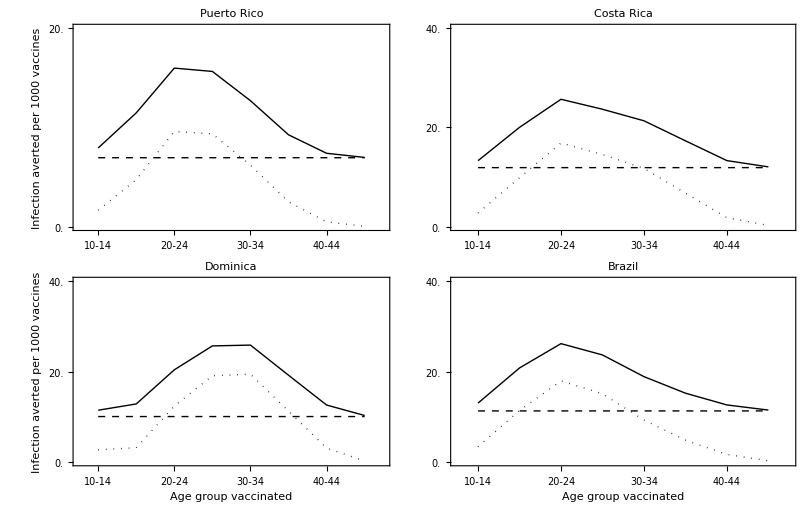

```mathematica
GraphicsGrid[{
{featurePlot["Puerto Rico",True,False,False],featurePlot["Costa Rica",False,True,False]},
{featurePlot["Dominica",True,False,True],featurePlot["Brazil",False,True,True]}
},Spacings->0]
```

## Figure 5 - Plot frontier

### Compute best fit hull/frontier for Puerto Rico

#### Read in results

No vaccine scenario

```mathematica
SetDirectory[NotebookDirectory[]<>"/GeneratedResults/AgeScenarios/"]
```

C:\Users\carbon\Dropbox\Code\Git\ZikaVaccineModel\GeneratedResults\AgeScenarios

```mathematica
noVaccineResult=Get["noVaccineResult_Puerto Rico_attR_0.25_lag_0.dat"];
```

Core scenarios

```mathematica
vaccResultsFrontier=Get["resultsFrontier_Puerto Rico_attR_0.25_lag_0.dat"];
```

#### Plot

```mathematica
computedResults=computedResultsFunction[noVaccineResult,vaccResultsFrontier];
```

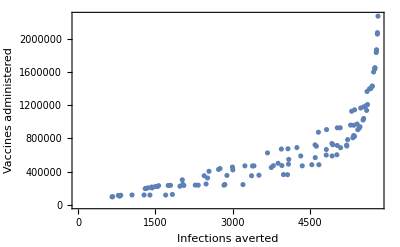

```mathematica
ListPlot[Tooltip[#[[;;2]],#[[3]]]&/@computedResults,Frame->{True,True,False,False},FrameLabel->{"Infections averted","Vaccines administered"}]
```

#### Compute convex hull

Compute the scenario with fewest number of vaccines administered

```mathematica
minVaccScen=MinimalBy[computedResults,Second]
```

{{660.657,97200.,0 to 4 Women}}

Extract subset remaining

```mathematica
computedResultsSubset=Complement[computedResults,minVaccScen];
```

```mathematica
minVaccScen[[1]]
```

{660.657,97200.,0 to 4 Women}

```mathematica
MinimalBy[Append[#,((#[[2]]-minVaccScen[[1,2]])/(#[[1]]-minVaccScen[[1,1]]))]&/@computedResultsSubset,Last]
```

{{1721.48,118800.,25 to 29 Women,21.3532}}

```mathematica
data=computeConvexHull[computedResults];
```

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
data[[;;2]]
```

{{660.657,97200.,0 to 4 Women},{1700.6,118800.,25 to 29 Women}}

```mathematica
data={#[[1]],#[[2]],
StringReplace[If[StringContainsQ[#[[3]],"Women"],"F "<>StringReplace[#[[3]]," Women"->""],"M/F "<>StringReplace[#[[3]]," All"->""]]," to "->"-"]}&/@data
```

{{660.657,97200.,F 0-4},{1700.6,118800.,F 25-29},{1831.54,126000.,F 20-24},{3201.27,244800.,F 20-29},{4065.62,363600.,F 20-34},{4674.29,483300.,F 15-34},{5023.58,603000.,F 15-39},{5216.39,708300.,F 10-39},{5365.76,824400.,F 10-44},{5457.54,923400.,F 5-44},{5471.38,939600.,F 10-49},{5531.01,1.0206×10^6,F 0-44},{5543.48,1.0386×10^6,F 5-49},{5600.73,1.1358×10^6,F 0-49},{5711.28,1.4274×10^6,M/F 10-39},{5763.62,1.6488×10^6,M/F 10-44},{5791.68,1.854×10^6,M/F 5-44},{5792.93,1.8648×10^6,M/F 10-49},{5809.17,2.0529×10^6,M/F 0-44},{5810.42,2.07×10^6,M/F 5-49},{5821.39,2.2689×10^6,M/F 0-49}}

```mathematica
leaderLength={{0,-100000},{0,-100000},{500,-250000},{350,-175000},{300,-110000},{200,-50000},{-200,-50000},{200,-50000},{-200,-75000},{200,-75000},{-400,0},{-300,150000},{150,0},{200,100000},{0,0},{0,0},{-400.,0.},{0.,0.},{-400,0},{0,0},{0,0}};

(*{{5000.,-480000.},{2700.,-320000.},{1300.,0.},{2700.,0.},{9200.,0.},{1,1},{6400.,0.},{1,1},{2300.,0.},{1300.,0.},{-500.,20000.},{1,1},{400.,-40000.},{-500.,20000.},{1800.,100000.},{900.,40000.},{-1400.,0.},{1,1}}*)(*Table[{1,1},Length@data]*)
```

### Plot frontier with variable labels

```mathematica
With[{len=100,xmin=-40000,ymin=-2500000,xmax=40000,ymax=2500000},
TabView[{
Slider2D[Dynamic@leaderLength[[1]],{{xmin,ymin},{xmax,ymax}}],
Slider2D[Dynamic@leaderLength[[2]],{{xmin,ymin},{xmax,ymax}}],
Slider2D[Dynamic@leaderLength[[3]],{{xmin,ymin},{xmax,ymax}}],
Slider2D[Dynamic@leaderLength[[4]],{{xmin,ymin},{xmax,ymax}}],
Slider2D[Dynamic@leaderLength[[5]],{{xmin,ymin},{xmax,ymax}}],
Slider2D[Dynamic@leaderLength[[6]],{{xmin,ymin},{xmax,ymax}}],
Slider2D[Dynamic@leaderLength[[7]],{{xmin,ymin},{xmax,ymax}}],
Slider2D[Dynamic@leaderLength[[8]],{{xmin,ymin},{xmax,ymax}}],
Slider2D[Dynamic@leaderLength[[9]],{{xmin,ymin},{xmax,ymax}}],
Slider2D[Dynamic@leaderLength[[10]],{{xmin,ymin},{xmax,ymax}}],
Slider2D[Dynamic@leaderLength[[11]],{{xmin,ymin},{xmax,ymax}}],
Slider2D[Dynamic@leaderLength[[12]],{{xmin,ymin},{xmax,ymax}}],
Slider2D[Dynamic@leaderLength[[13]],{{xmin,ymin},{xmax,ymax}}],
Slider2D[Dynamic@leaderLength[[14]],{{xmin,ymin},{xmax,ymax}}],
Slider2D[Dynamic@leaderLength[[15]],{{xmin,ymin},{xmax,ymax}}],
Slider2D[Dynamic@leaderLength[[16]],{{xmin,ymin},{xmax,ymax}}],
Slider2D[Dynamic@leaderLength[[17]],{{xmin,ymin},{xmax,ymax}}],
Slider2D[Dynamic@leaderLength[[18]],{{xmin,ymin},{xmax,ymax}}],
Slider2D[Dynamic@leaderLength[[19]],{{xmin,ymin},{xmax,ymax}}],
Slider2D[Dynamic@leaderLength[[20]],{{xmin,ymin},{xmax,ymax}}],
Slider2D[Dynamic@leaderLength[[21]],{{xmin,ymin},{xmax,ymax}}]}]
]
```

123456789101112131415161718192021

Use the 2d slider bars above to adjust the position of each of the 18 labels

```mathematica
leaderLength[[5]]={300,-110000}
```

{300,-110000}

```mathematica
Dynamic@ListPlot[{
computedResults[[All,;;2]],
Table[Callout[
Style[data[[hull,;;2]],If[StringContainsQ[data[[hull,3]],"M/F"],Black,Red]],
StringSplit[data[[hull,3]]," "][[2]],
data[[hull,;;2]]+leaderLength[[hull]]],
{hull,Length@data}]},
Frame->{True,True,False,False},FrameLabel->{"Infections averted","Vaccines administered"},FrameStyle->Black,FrameTicks->{{Range[0,2500000,500000],None},{Range[0,35000,5000],None}},
PlotRange->{{0,10000},{-500000,2500000}},PlotStyle->{GrayLevel[0.75],Black}]
```